```mathematica
dir="/Users/Simon/Code/cytoMod/shila/";
f1="linkStiffness1/txt_files/angle_correlations.txt";
f2="linkStiffness10/txt_files/angle_correlations.txt";
f3="linkStiffness100/txt_files/angle_correlations.txt";
```

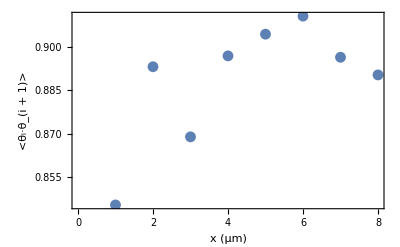

```mathematica
d1=ReadList[dir<>f1,Number, RecordLists->True];
ListPlot[d1,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 1 pN/μm;nmonomers = 10"}]
```

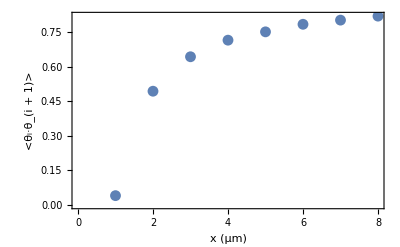

```mathematica
d2=ReadList[dir<>f2,Number, RecordLists->True];
ListPlot[d2,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 10 pN/μm; nmonomers=10"}]
```

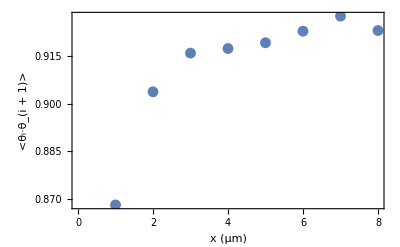

```mathematica
d3=ReadList[dir<>f3,Number, RecordLists->True];
ListPlot[d3,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 100 pN/μm; nmonomers = 10"}]
```

```mathematica
f4="kl1_nm100/txt_files/angle_correlations.txt";
f5="kl10_nm100/txt_files/angle_correlations.txt";
f6="kl100_nm100/txt_files/angle_correlations.txt";
```

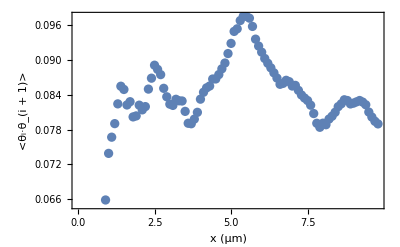

```mathematica
d4=ReadList[dir<>f4,Number, RecordLists->True];
ListPlot[d4,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 1 pN/μm; nmonomers = 100"}]
```

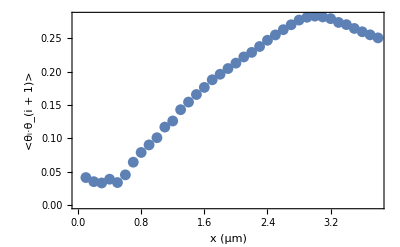

```mathematica
d5=ReadList[dir<>f5,Number, RecordLists->True];
ListPlot[d5,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 10 pN/μm; nmonomers = 100"}]
```

```mathematica
d6=ReadList[dir<>f6,Number, RecordLists->True];
ListPlot[d6,Frame->True, FrameLabel->{"x (μm)","<θ_i·θ_(i + 1)>","link stiffness = 100 pN/μm; nmonomers = 100"}]
```

ReadList::readn: Invalid real number found when reading from "/Users/Simon/Code/cytoMod/shila/kl100_nm100/txt_files/angle_correlations.txt".

-Graphics-